# The Duffing Equation

## Introduction

We have already seen that chaotic behavior can emerge in a system as simple as the logistic map. In that case the "route to chaos" is called period-doubling.  In practice one would like to understand the route to chaos in systems described by partial differential equations, such as flow in a randomly stirred fluid. This is, however, very complicated and difficult to treat either analytically or numerically. Here we consider an intermediate situation where the dynamics is described by a single ordinary differential equation, called the Duffing equation. 

In order to get chaos in such a simple system, we will need to add both a driving force and friction. First of all though we just consider the basic equation without these extra features. The Duffing equation describes the motion of a classical particle in a double well potential. We choose the units of length so that the minima are at x = ± 1, and the units of energy so that the depth of each well is at -1/4. The potential is given by

V(x) = -x^2/2 + x^4/4

Let's plot this:

```mathematica
Clear["Global`*"]
```

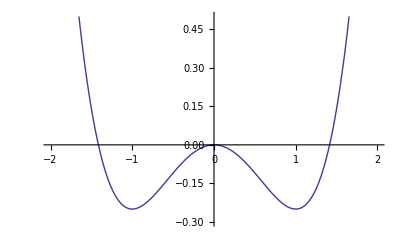

```mathematica
Plot[-x^2/2+x^4/4,{x,-2,2}, PlotRange -> {-0.3, 0.5}]
```

The force is given by F(x) = -dV/dx = x - x^3.  As usual we solve the second order differential equation F = ma by expressing it as two first order differential equations, v = dx/dt, mdv/dt = F.  From now on we set the mass equal to unity so we have.

dx/dt = v ,       dv/dt= x - x^3.

Let us first use the Mathematica function NDSolve to solve the equation starting the particle at the right-hand minimum, x=1, with velocity equal to 1. This is big enough to kick the particle over the hump in the potential energy at x=0 to the vicinity of the x=-1 minimum and back again. Why? (You should easily be able to show from energy conservation that the particle will get over the hump if the initial velocity is greater than 1/√2.)

```mathematica
sol1 = NDSolve[ {v'[t] == x[t] - x[t]^3, x'[t] == v[t], x[0]== 1, 
      v[0] == 1}, {x, v}, {t, 0, 10} ];
```

It is convenient to present the results as a "phase space" plot, where the axes are v and x. This is shown below for t between 0 and 10.

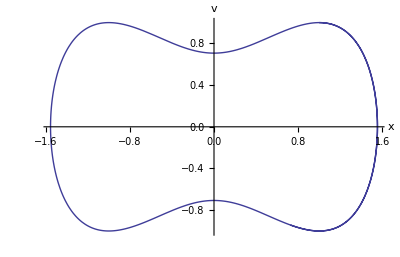

```mathematica
ParametricPlot[{x[t],v[t]}/.sol1,{t,0,10},AxesLabel->{"x","v"}]
```

You see that the phase space trajectory closes on itself. In fact this must be so since energy is conserved, i.e. v^2/2 -x^2/2+ x^4/4 is constant, so if x is given then so is v, up to a sign. You can experiment by changing the time up to which you integrate in order to determine the time to go round the orbit once (the period) and to verify that at longer times than this the motion just repeats.

## Forcing and Damping; periodic orbits

Because of energy conservation one can clearly never get chaos from the motion of a single degree of freedom. We therefore add both a driving force and damping, in order to remove energy conservation. The equations of motion are then

dx/dt = v ,    dv/dt = x - x^3- γv + d cos(ωt)

where γ is the friction coefficient, and d is the strength of the driving force which oscillates at a frequency ω.  We will see that a transition to chaos now occurs as the strength of the driving force is increased. We will fix γ = 0.1 and ω = 1.4, and initially set d = 0.1 (which will be in the non-chaotic regime).

```mathematica
γ = 0.1; d = 0.1; ω = 1.4;
```

We now start the particle off at rest at the origin and integrate the equations of motion . We will go up to t = 200. In order to have sufficient accuracy we need to set the option MaxSteps of NDSolve to a larger value than the default (otherwise Mathematica will grumble).

```mathematica
sol2 = NDSolve[ {v'[t] == x[t] - x[t]^3 - γ v[t] + d Cos[ω t], 
      x'[t] == v[t], x[0]== 0, v[0] == 0}, {x, v}, {t, 0, 200}, 
    MaxSteps -> 3500 ];
```

We  now show a phase space plot of the trajectory:

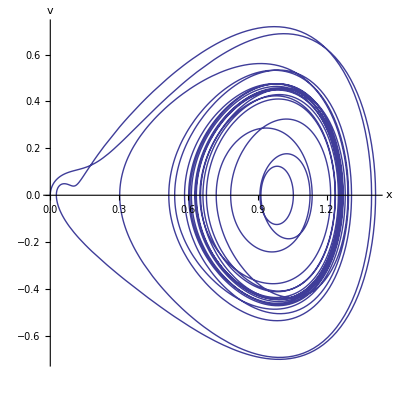

```mathematica
ParametricPlot[{x[t],v[t]}/.sol2,{t,0,100},AxesLabel->{"x","v"}]
```

This looks complicated, but in fact, most of the plot shows the initial period of time during which the motion is approaching its final behavior which is much simpler. The early behavior is called an "initial transient". To see that this is the case, let's just look at the behavior for t at later times between 150 and 200.

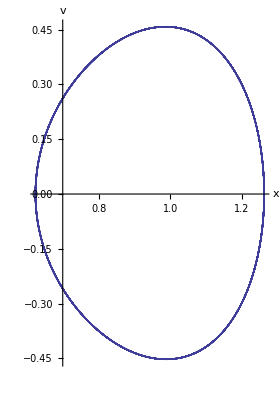

```mathematica
ParametricPlot[{x[t],v[t]}/.sol2,{t,150,200},AxesLabel->{"x","v"}]
```

One now sees a simple periodic orbit. around the minimum of the potential at x = 1. The period of the orbit is just 2 π / ω = 4.48799..., the period of the driving force. One can verify this by integrating for different periods of time. The figure below integrates over a time range of 4.46, and shows that the orbit is not quite completed, as expected.

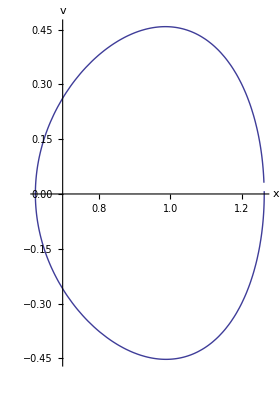

```mathematica
ParametricPlot[{x[t],v[t]}/.sol2,{t,150,154.46},AxesLabel->{"x","v"}]
```

## Transition to Chaos

We now investigate how the phase space plots change when the strength of the driving force is changed. It is convenient to define a function, which we call "solution[d, tmax]" , which will integrate the equations for a given value of the forcing, d, up to a time tmax. We use a delayed assignment because we want the evaluation only to be done when we call the function later with particular values of d and tmax.

```mathematica
Clear[d];
```

```mathematica
solution[ d_, tmax_] := 
  NDSolve[ {v'[t] == x[t] - x[t]^3 - γ v[t] + d Cos[ω t], 
      x'[t] == v[t], x[0]== 0, v[0] == 0}, {x, v}, {t, 0, tmax}, 
    MaxSteps -> 100 tmax ]
```

First we choose d = 0.32 and tmax = 800.

```mathematica
sol3 = solution [ 0.32, 800 ];
```

To plot the solution,  it is convenient to first define a function "graph[tmin, tmax]" which plots the solution between tmin and tmax:

```mathematica
graph[tmin_, tmax_] := 
  ParametricPlot[ {x[t], v[t]} /. sol3, {t, tmin, tmax},
    AxesLabel -> {"x", "v"} ]
```

Up to t = 200 the motion looks complicated, see below.

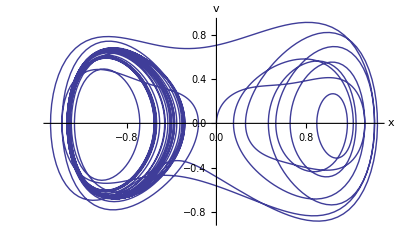

```mathematica
graph[0, 200]
```

Note that the particle has moved through both of the wells. However, again, most of this complexity is due to an initial transient. If we look at the behavior at later times, we take from 750 to 800, we see a much simpler curve:

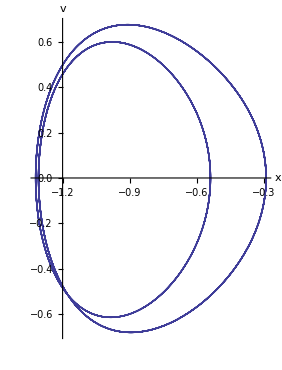

```mathematica
graph[750, 800]
```

The particle settles down in the vicinity of the x = -1 minimum and, once it has done so, goes twice around x=-1, v=0 before retracing its path. In fact the period has doubled to 4π/ω as can be checked by trial and error. Depending on the exact value of d and the initial conditions the particle could, alternatively, have gone into a period doubled orbit near the other minimum at x = +1. 

Next let's increase the driving force to 0.338.

```mathematica
sol3 = solution [ 0.338, 2000 ];
```

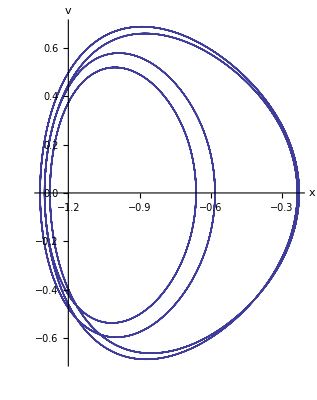

```mathematica
graph[1900, 2000]
```

The orbit now goes 4 times round the point x = 1 before repeating. One might expect that the period has doubled again, and this is indeed the case. We have started a period doubling sequence of "bifurcations" that we first met in the logistic map.  Next we increase driving force to 0.35.

```mathematica
sol3 = solution [ 0.35, 3000];
```

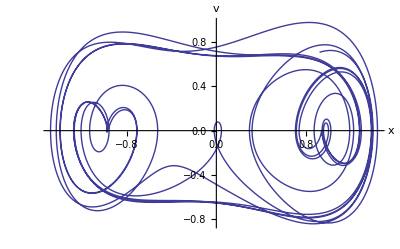

```mathematica
graph[2900, 3000]
```

Now there is no sign of the data settling down to a periodic orbit. The motion is chaotic. A more detailed study shows that a period doubling transition to chaos occurs just as in the logistic map. Furthermore, the value of the Feigenbaum constant δ is the same as in the logistic map, even though the models are completely different. This is expected from the claimed “universality” of the Feigenbaum constant.

## Poincaré Sections

A useful way of analyzing chaotic motion is to look at what is called the Poincaré section. Rather than considering the phase space trajectory for all times, which gives a continuous curve, the Poincaré section is just the discrete set of phase space points of the particle at every period of the driving force, i.e. at t = 2π/ω, 4π/ω, 6π/ω, etc. Clearly for a periodic orbit the Poincaré section  is a single point, when the period has doubled it consists of two points, and so on.

We define a function, "poincare", which produces a Poincaré section for given values of d, γ, and ω, in which the first "ndrop" periods are assumed to be initial transient and so are not plotted, while the subsequent "nplot" periods are plotted. The point size is given by the parameter "psize". 

Note that the function g[{xold, vold}] maps a point in phase space {xold, vold} at time t to the point in phase space {x, v} one period T later. 

This map is then iterated with NestList.

```mathematica
poincare[d_,γ_,ω_,ndrop_,nplot_,psize_]:=(T=2 π/ω;g[{xold_,vold_}]:={x[T],v[T]}/.NDSolve[{v'[t]==x[t]-x[t]^3-γ v[t]+d Cos[ω t],x'[t]==v[t],x[0]==xold,v[0]==vold},{x,v},{t,0,T}][[1]];
lp=ListPlot[Drop[NestList[g,{0,0},nplot+ndrop],ndrop],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"x","v"}])
```

If we put in parameters corresponding to a limit cycle of length 4 we get 4 points as expected.

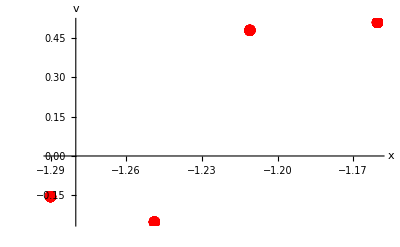

```mathematica
poincare[0.338,0.1,1.4,1900,100,0.02]
```

## Strange attractor

However,the Poincaré section for parameters in the chaotic regime is much richer. Here we take d = 0.35,

```mathematica
poincare [ 0.35, 0.1, 1.4, 200, 15000, 0.002];
```

The semicolon means that the graphics object lp will not be displayed. It will be plotted in the next command, with some additional plot options, using  Show:

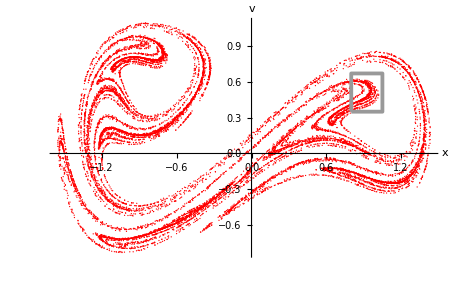

```mathematica
Show[lp,Epilog->{GrayLevel[0.6],Thickness[0.006],Line[{{0.8,0.35},{0.8,0.67},{1.05,0.67},{1.05,0.35},{0.8,0.35}}]}]
```

This strange diagram is the strange attractor. It is the limiting set of points to which the trajectory tends (after the initial transient) every period of the driving force.  Notice the that the attractor is complicated but not completely random, we see structure.  

We now want to study the structure of the strange attractor in more detail. To do this we will blow up the region in the shaded box in the above figure. To do so,  we define a function poincare2, in which we specify the range of x and v to be included in the plot:

```mathematica
poincare2[d_, γ_, ω_, ndrop_, nplot_, psize_, xmin_, xmax_, vmin_, vmax_] := (
T = 2 π/ω; g[{xold_, vold_}] := {x[T], v[T]} /. 
	NDSolve[ {v'[t] == x[t] - x[t]^3 - γ v[t] + d Cos[ω t],
		x'[t] == v[t], x[0] == xold, v[0] == vold}, 
				{x, v}, {t, 0, T} ] [[1]] ;
lp2 = ListPlot[ Drop[ NestList[g, {0, 0}, nplot+ndrop],ndrop],PlotRange -> {{xmin, xmax}, {vmin, vmax}},
    PlotStyle ->{ PointSize[psize],Hue[0]}, PlotRange -> All,
			AxesLabel -> {"x", "v"} , AxesOrigin -> {xmin, vmin}, AspectRatio -> 1 ])
```

We zoom in to the region marked by the box in the figure above (this is quite slow because I had to increase the time of integration to 10^5 to get enough points in this region)

```mathematica
poincare2[0.35, 0.1, 1.4, 2000, 100000, 0.003, 0.8, 1.05, 0.35, 0.67];
```

The plot is then displayed including a box to indicate the region that will subsequently be blown up even more.

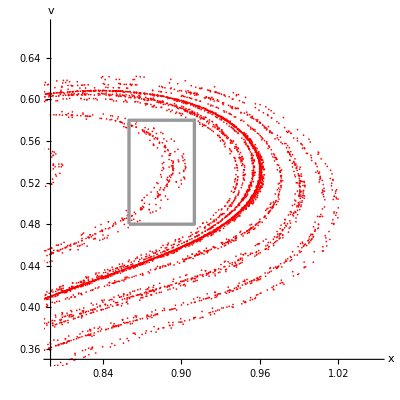

```mathematica
Show[lp2,Epilog->{GrayLevel[0.6],Thickness[0.006],Line[{{0.86,0.48},{0.91,0.48},{0.91,0.58},{0.86,0.58},{0.86,0.48}}]}]
```

Zooming in to the region in the box in the above figure, shows many of the same features as in the figure. (This takes a very long time, because I had to increase the length of the integration to 10^6 to get a significant density of points in this small region. You may want to skip the execution of the rest of this notebook, and just look at it.)

```mathematica
poincare2[0.35, 0.1, 1.4, 2000, 1000000, 0.005, 0.86, 0.91, 0.48, 0.58];
```

```mathematica
Show[lp2,Epilog->{GrayLevel[0.6],Thickness[0.006],Line[{{0.88,0.525},{0.88,0.55},{0.888,0.55},{0.888,0.525},{0.88,0.525}}]}]
```

-Graphics-

Note the boxed region, which is very similar to the boxed region in the figure above it, and which can be blown up again to reveal the same features on a still smaller scale. (I presume; it would have taken too much CPU time and memory to check it.)

Having the same features appearing in different parts of a figure and at different scales is a characteristic feature of a fractal.

Integrating a differential equation, as we have done here, is much more time consuming than iterating a map, such as the logistic map. People have therefore investigated maps which have similar behavior to that of driven, damped differential equations like the Duffing equation.  One popular choice is the  Hénon map:

x_(n+1)= 1  -  a x_n^2 + y_n
y_(n+1) = b x_n

in which two variables, x and y, are iterated. The parameters a and b can be adjusted to get a transition to chaos. In the chaotic regime the points to converge to a strange attractor similar to the one found for the Duffing equation. Note, in particular, the way it folds back on itself.  A discussion of using Mathematica to display the Hénon map is given in Zimmerman and Olness, Mathematica for Physics, p. 289.

## More on the transition to chaos

Going back to the Duffing equation, you can try different values of the parameters γ and ω and see where the period doubling transition to chaos occurs. The function bifurcation below, is similar to poincare except that it scans a range of values of d, and gives the x-values on the attractor for each d. (It can take a long time to execute).

```mathematica
bifurcation[dmin_,dmax_,nd_,xmin_,xmax_,γ_,ω_,ndrop_,nplot_,psize_]:=(T=(2 π)/ω;xi = 1; vi = 0;g[{xold_,vold_}]:={x[T],v[T]}/.NDSolve[{v'[t]==x[t]-x[t]^3-γ v[t]+d Cos[ω t],x'[t]==v[t],x[0]==xold,v[0]==vold},{x,v},{t,0,T}]⟦1⟧;f[{x_,y_}]:=(xi = x; vi = y;{d,x});ListPlot[Flatten[Table[f/@Drop[NestList[g,{xi,vi},nplot+ndrop],ndrop],{d,dmin,dmax,(dmax-dmin)/nd}],1],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->{{dmin,dmax},{xmin,xmax}},AxesLabel->{"d","x"}])
```

The command Flatten[ ... , 1] removes one layer of curly brackets. (Without that we would have separate lists for each value of d. Flatten[ ... 1] gives us one long list, each element of which is a list comprising a pair of points in (d, x) space which is to be plotted.) The syntax f /@ list is equivalent to Map[f, list], i.e. apply the function f to each element of list. The range of the plot is from dmin to dmax in the horizontal direction, and from xmin to xmax (also arguments to the function) in the vertical direction.

The following command scans 200 values of d in the range from 0.3 to 0.35, with γ =0.1 and ω =1.4. It starts with v=0 and x=1, i.e.at rest in the x=1 minimum.The equations are integrated for 2000 periods of the driving force with the first 1000 being ignored and the value of x plotted at the end of each of the remaining 1000 periods. (This is very slow)

```mathematica
bifurcation[0.30, 0.35, 200, 0.1, 0.8, 0.1, 1.4, 2000, 1000,0.006]
```

-Graphics-

One clearly sees period doubling leading into chaos. I should mention that, for Poincaré sections in this region of d, the system is either in the vicinity of the well at positive x or in the vicinity of the the well at negative x, depending on the initial values for x and v and the precise value of d, but does not hop between wells. For example, for d < 0.309 there are actually two separate fixed points. When plotting the figure, it is convenient that the system is always in the vicinity of the same well, so I start the system off at the next value of d with the final values of x and v from the previous value of d.  As a result, in the above figure,  the system is in the positive x region for all d for the discrete times used to generate the Poincaré section. 

The Feigenbaum constant is the ratio of the range over which a limit cycle has a certain period, to the range where the period is doubled. Being universal, it is expected to have the same value, 4.6692..., in this period doubling route to chaos (which comes from a differential equation), as it has in the logistic map (which  involves iterating a map). This is a remarkable result, which is expected to be true, but I have not seen it demonstrated explicitly.

In order to estimate the Feigenbaum constant for the Duffing equation,  I zoomed in to the later stages of the period doubling route to chaos, and show the results below. It turns out that for this starting value of d in the figure, 0.334,  the system is near the minimum at negative x at the times taken to generate the Poincaré section, and so we just plot this region.

```mathematica
bifurcation[0.334, 0.342, 200, -1.35, -1.1,0.1, 1.4, 5000, 1000, 0.006]
```

-Graphics-

From the two previous figures I estimate four period doublings to occur at

```mathematica
d[1] = 0.3084; d[2] = 0.3358; d[3] = 0.3396; d[4] = 0.3402;
```

```mathematica
Print [ k, "       ", Subscript[δ, k]]; 
Do[ Print[n , "      ", ( d[n] - d[n-1])/(d[n+1] - d[n])], {n, 2, 3}]
```

k       δ_k

2      7.21053

3      6.33333

It is possible that these values tend to the Feigenbaum value 4.6692 ... for large k, but it seems to be quite challenging numerically to demonstrate this convincingly since it would require going to several more levels of period doubling. A motivated student might like to investigate this question. 

Incidentally, you may ask how I determined these values for d[k] to 4-digit precision from the graph. This is possible because Mathematica can display the coordinates of the location of the cursor on a graph.  To do this, select the graph, then select “Drawing Tools” from the Graphics menu, and then click on the “Get Coordinates Tool”.  Now, when you move the cursor over the plot you see the x and y coordinates.